# New analytic formulae for memory and prediction functions in reservoir computers with time delays

Abstract :
 Time delays increase the effective dimensionality of reservoirs, thus suggesting that time delays in reservoirs can enhance their performance, particularly their memory and prediction abilities . We find new closed - form expressions for memory and prediction functions of linear time - delayed reservoirs in terms of the power spectrum of the input and the reservoir transfer function . We confirm this relationship numerically for some time - delayed reservoirs using simulations, including when the reservoir can be linearized but is actually nonlinear . Finally, we use these closed - form formulae to address the utility of multiple time delays in linear reservoirs in order to perform memory and prediction, finding similar results to previous work on nonlinear reservoirs . We hope these closed - form formulae can be used to understand memory and predictive capabilities in time - delayed reservoirs .

## Part 1 of Figure 4

The code below simulates a linear reservoir with chosen delays, measures how well s predicts x across time lags using R.b2, and plots the results to compare the no-delay, single-delay, and multi-delay cases .
- Simulates a noisy, damped oscillator as the input signal.
- Processes it with three linear reservoir setups: no delay, a single delay, and multiple delays.
- Computes a memory function by fitting x shifted in time from s and recording R.b2 across lags.
- Plots the three curves to compare how delays affect memory.

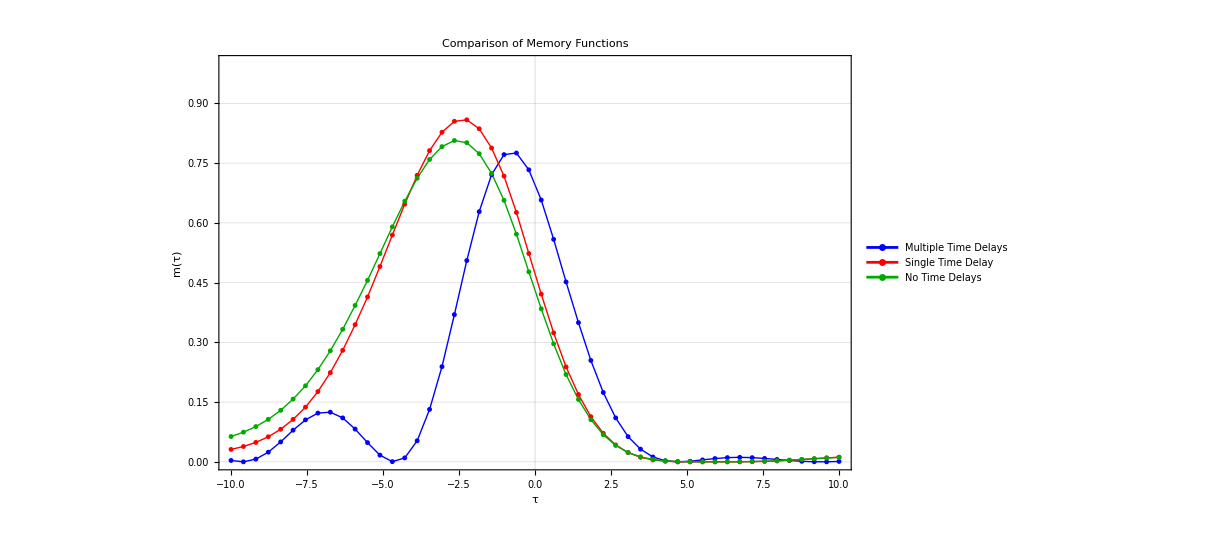

```mathematica
(*Parameters and grids*)
alpha=0.2;gamma=0.5;dD=1.;k=0.2;
dt=0.01;sdt=Sqrt[dt];
T=200.;numSteps=Floor[T/dt];
tauValues=Subdivide[-10.,10.,49];

(*Fixed randomness so runs are reproducible and comparable*)
SeedRandom[12345];
etaMaster=RandomVariate[NormalDistribution[0,1],numSteps-1];
(*Simulator:noisy SHO driving a linear delayed reservoir*)
simulateLinearWithEta[delays_List,eta_List]:=Module[{delaySteps=Round[delays/dt],x,v,s,i,d},x=ConstantArray[0.,numSteps];v=ConstantArray[0.,numSteps];
s=ConstantArray[0.,numSteps];
Do[x[[i]]=x[[i-1]]+v[[i-1]]*dt;
(*Euler–Maruyama updates for x,v (noisy damped oscillator)*)
v[[i]]=v[[i-1]]+(-alpha*x[[i-1]]-gamma*v[[i-1]])*dt+eta[[i-1]]*dD*sdt;
If[delaySteps==={}||delaySteps==={0},
(*NO delay case*)s[[i]]=s[[i-1]]-k*(s[[i-1]]-x[[i]])*dt,
(*MULTI/SINGLE delay cases*)s[[i]]=s[[i-1]];
Do[If[i>d,s[[i]]+=(-k*(s[[i-d]]-x[[i]])*dt),Break[]],{d,delaySteps}]];,{i,2,numSteps}];
{x,s}];
(*Memory curve:R^2 between s(t) and time-shifted x*)
memoryR2FromSeries[x_List,s_List]:=Table[With[{steps=Floor[Abs[tau]/dt]},Module[{delayedX,sShort,lm},
(*tau≥0 compares s(t) to FUTURE x(t+tau);tau<0 compares to PAST x(t-tau).*)If[tau>=0,delayedX=x[[1+steps;;]];sShort=s[[;;-1-steps]],delayedX=x[[;;-1-steps]];sShort=s[[1+steps;;]]];
lm=LinearModelFit[Transpose[{sShort,delayedX}],y,y];
lm["RSquared"]]],{tau,tauValues}];

(*run with the shared noise so only delays differ*)
computeMemory[delays_List]:=Module[{x,s},{x,s}=simulateLinearWithEta[delays,etaMaster];
memoryR2FromSeries[x,s]];

mMulti=computeMemory[{1.,2.,3.}];
mSingle=computeMemory[{1.}];
mNone=computeMemory[{}];

(*Plot*)
ListLinePlot[{Transpose[{tauValues,mMulti}],Transpose[{tauValues,mSingle}],Transpose[{tauValues,mNone}]},Joined->True,PlotMarkers->{{"●",5},{"●",5},{"●",5}},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick],Directive[Darker[Green],Thick]},Frame->True,GridLines->{{0},Automatic},PlotRange->{0,1},FrameLabel->{Style["τ",16],Style["m(τ)",16]},PlotLegends->Placed[{"Multiple Time Delays","Single Time Delay","No Time Delays"},{Right,Center}],PlotLabel->Style["Comparison of Memory Functions",24,Bold],ImageSize->900]
```

Below produces a  “memory function” 𝑚(𝜏) using the analytic formula for m (τ) in Eq . 13 of the paper for a linear delayed reservoir with multiple time delays driven by a noisy damped oscillator, then plots m(τ) over 𝜏 ∈ [−10,10].

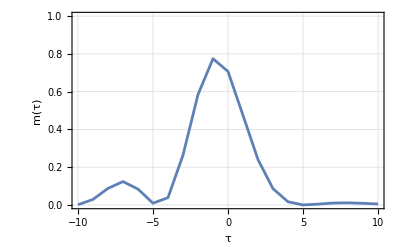

```mathematica
alpha=0.2;k=0.2;d=1;gamma=0.5;

newint[tt_]:=ComplexExpand[Re[Exp[-I*ω*tt]*(1*3*(d^2/((ω^2-alpha)^2+ω^2*gamma^2)))/(I*ω+k*(Exp[-I*ω*1]+Exp[-I*ω*2]+Exp[-I*ω*3]))]];

numerator[tt_]:=(1/(2*Pi))^2*Re[NIntegrate[Evaluate[newint[tt]],{ω,-∞,∞}]]^2

denominator=(1/(2*Pi))*Re@NIntegrate[(1*3)^2*(d^2/((ω^2-alpha)^2+ω^2*gamma^2))/Abs[I*ω+k*(Exp[-I*ω*1]+Exp[-I*ω*2]+Exp[-I*ω*3])]^2,{ω,-∞,∞}]*(1/(2*Pi))*NIntegrate[d^2/((ω^2-alpha)^2+ω^2*gamma^2),{ω,-∞,∞}];

data=Table[{T,numerator[T]/denominator},{T,-10,10}];
ListPlot[data,Joined->True,PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"τ","m(τ)"}]
```

## Figure 1

Below I overlay the empirical memory function with the analytic memory function for a linear reservoir with multiple time delays. This code produced Figure 1 in the paper. The plot shows that the analytics match the simulation results.

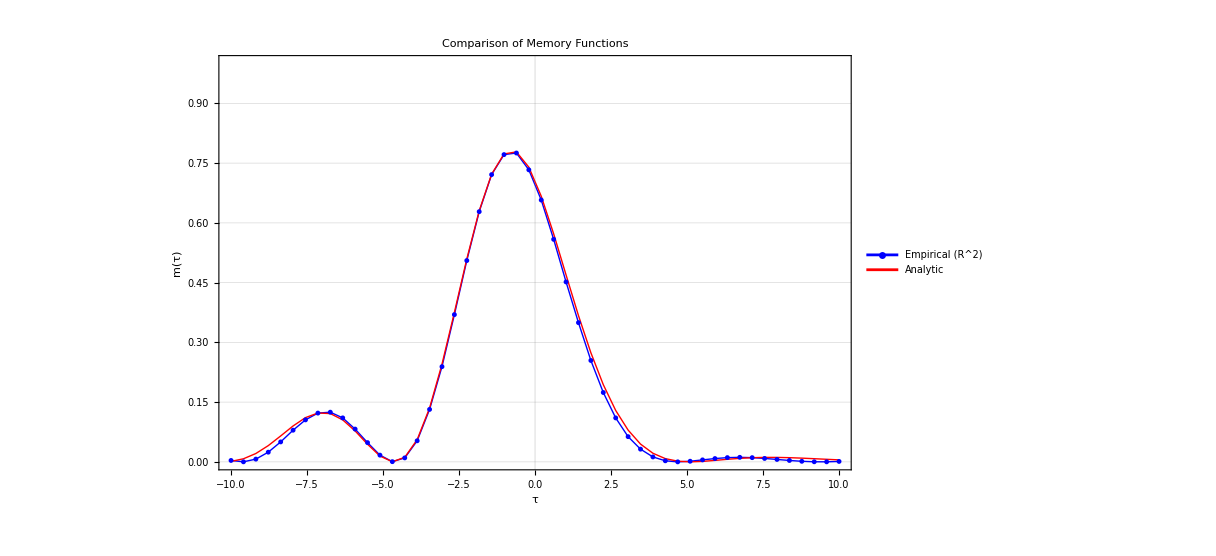

```mathematica
analyticOnGrid=Transpose@{tauValues,(numerator[#]/denominator)&/@tauValues};

empirical=Transpose@{tauValues,mMulti};    

ListLinePlot[{empirical,analyticOnGrid},Joined->True,PlotMarkers->{{"●",5},None},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},Frame->True,GridLines->{{0},Automatic},PlotRange->{0,1},FrameLabel->{Style["τ",16],Style["m(τ)",16]},PlotLegends->Placed[{"Empirical (R^2)","Analytic"},{Right,Center}],PlotLabel->Style["Comparison of Memory Functions",24,Bold],ImageSize->900]
```

## Figure 2

Below calculates uses the analytics to produce the memory function for a linear reservoir with an irrational time delay (π ) . This proved that the analytic formula for m (τ) in Eq . 13 of the paper, the memory and prediction function, can handle irrational time delays that would be hard to simulate . Irrational time delays technically lead to an infinite - order reservoir and involve propagating a function rather than a finite number of values . Reservoir and input have parameters k = 0.2, K = 0.2, D = 1, γ = 0.5, and a time delay of π . This produced Figure 2!

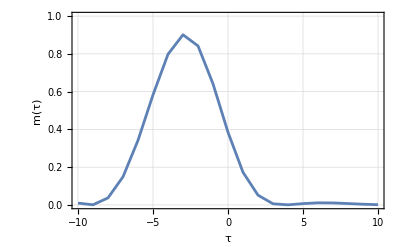

```mathematica
ClearAll["Global`*"];

alpha=0.2;k=0.2;d=1;gamma=0.5;

newint[tt_]:=ComplexExpand[Re[Exp[-I*ω*tt]*(1*3*(d^2/((ω^2-alpha)^2+ω^2*gamma^2)))/(I*ω+k*(Exp[-I*ω*π]))]];

numerator[tt_]:=(1/(2*Pi))^2*Re[NIntegrate[Evaluate[newint[tt]],{ω,-∞,∞}]]^2

denominator=(1/(2*Pi))*Re@NIntegrate[(1*3)^2*(d^2/((ω^2-alpha)^2+ω^2*gamma^2))/Abs[I*ω+k*(Exp[-I*ω*π])]^2,{ω,-∞,∞}]*(1/(2*Pi))*NIntegrate[d^2/((ω^2-alpha)^2+ω^2*gamma^2),{ω,-∞,∞}];

data=Table[{T,numerator[T]/denominator},{T,-10,10}];
ListPlot[data,Joined->True,PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"τ","m(τ)"}]
```

## Figure 3

Below is a simulation of a nonlinear reservoir with multiple time delays, as well as code to calculate the approximated memory function for the nonlinear reservoir with multiple time delays. I then overlay my simulated memory function and my approximated memory function to produced Fig . 3. This showed that the analytics match the simulation results even for nonlinear reservoirs that can be linearized.

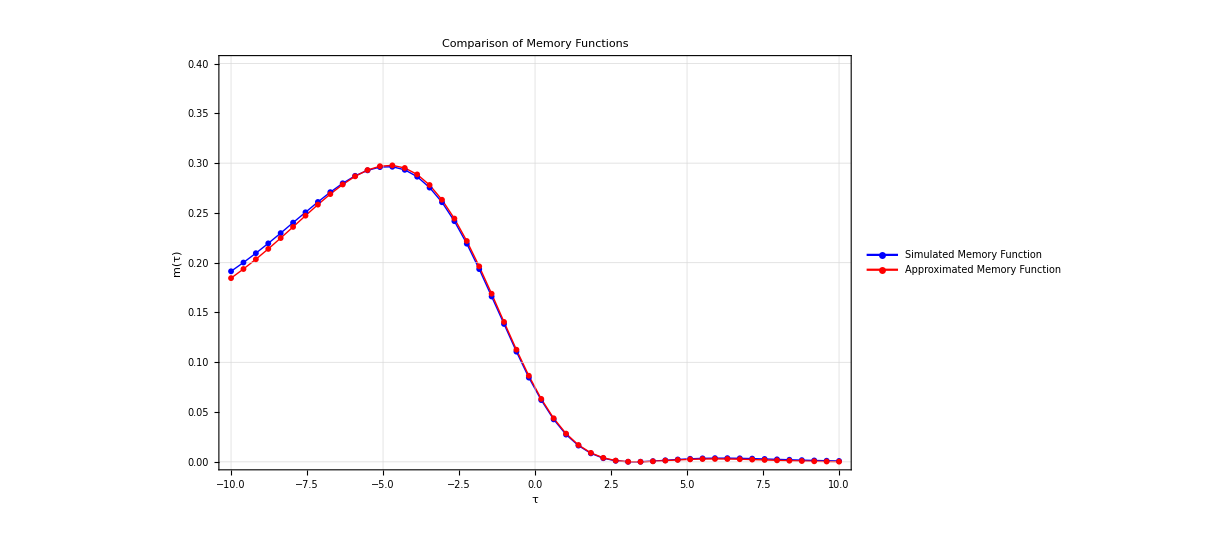

```mathematica
ClearAll["Global`*"];

alpha=0.2;beta=0.05;gamma=0.5;dD=1.0;k=0.2;
dt=0.01;sqrtDt=Sqrt[dt];

T=10000.0;
numSteps=Floor[T/dt];

delays={1.0,2.0,3.0};
delaySteps=Developer`ToPackedArray@Sort@Round[delays/dt];

target=If[MemberQ[$AvailableCompilationTargets,"C"],"C","WVM"];

(*simulation*)
simNonlinearXS=Compile[{{alpha,_Real},{beta,_Real},{gamma,_Real},{dD,_Real},{k,_Real},{dt,_Real},{sqrtDt,_Real},{delaySteps,_Integer,1},{eta,_Real,1},{numSteps,_Integer}},Module[{x,v,s,xs,i,j,nd,sumTanh},x=ConstantArray[0.,numSteps];
v=ConstantArray[0.,numSteps];
s=ConstantArray[0.,numSteps];
xs=ConstantArray[0.,{numSteps,2}];
nd=Length[delaySteps];
xs[[1,1]]=0.;xs[[1,2]]=0.;
For[i=2,i<=numSteps,i++,(*SHO input dynamics*)x[[i]]=x[[i-1]]+v[[i-1]]*dt;
v[[i]]=v[[i-1]]+(-alpha*x[[i-1]]-gamma*v[[i-1]])*dt+dD*sqrtDt*eta[[i-1]];
(*nonlinear reservoir:single update,sum tanh over delays*)sumTanh=0.;
For[j=1,j<=nd,j++,If[i>delaySteps[[j]],sumTanh=sumTanh+Tanh[beta*(s[[i-delaySteps[[j]]]]-x[[i]])];];];
s[[i]]=s[[i-1]]-k*sumTanh*dt;
xs[[i,1]]=x[[i]];
xs[[i,2]]=s[[i]];];
xs],CompilationTarget->target,RuntimeOptions->"Speed",CompilationOptions->{"InlineExternalDefinitions"->True}];

(*tau grid and correlation helper*)
tauValues=Subdivide[-10.,10.,49];

rSquared[τ_?NumericQ]:=Module[{steps=Floor[Abs[τ]/dt],nEff,xShift,sShort,c},nEff=n-steps;
If[nEff<=0,Return[Indeterminate]];
If[steps==0,xShift=x;sShort=s,If[τ>0,xShift=x[[steps+1;;n]];sShort=s[[1;;nEff]],xShift=x[[1;;nEff]];sShort=s[[steps+1;;n]]]];
c=Correlation[sShort,xShift];
If[NumericQ[c],c^2,0.]];

(*run with a fixed RNG state*)
BlockRandom[SeedRandom[12345];
eta=Developer`ToPackedArray@N@RandomVariate[NormalDistribution[0.,1.],numSteps-1];
xs=simNonlinearXS[alpha,beta,gamma,dD,k,dt,sqrtDt,delaySteps,eta,numSteps];
x=xs[[All,1]];s=xs[[All,2]];
n=Length[x];
mTauValues=rSquared/@tauValues;];

(*analytics*)
d=1.;  

newint[tt_]:=ComplexExpand@Re[Exp[-I*ω*tt]*(beta*Length[delays]*(d^2/((ω^2-alpha)^2+ω^2*gamma^2)))/(I*ω+k*beta*Total[Exp[-I*ω*#]&/@delays])];

numerator[tt_]:=(1/(2*Pi))^2*Re@NIntegrate[Evaluate[newint[tt]],{ω,-∞,∞}]^2;

denominator=(1/(2*Pi))*NIntegrate[(beta*Length[delays])^2*(d^2/((ω^2-alpha)^2+ω^2*gamma^2))/Abs[I*ω+k*beta*Total[Exp[-I*ω*#]&/@delays]]^2,{ω,-∞,∞}]*(1/(2*Pi))*NIntegrate[d^2/((ω^2-alpha)^2+ω^2*gamma^2),{ω,-∞,∞}];

mAnalytic[τ_]:=numerator[τ]/denominator;

(*overlay plot*)
empData=Transpose[{tauValues,mTauValues}];
anData=Transpose[{tauValues,mAnalytic/@tauValues}];

blueMarker={Graphics[{Blue,EdgeForm[None],Disk[]}],6};
redMarker={Graphics[{Red,EdgeForm[None],Disk[]}],6};

ListLinePlot[{empData,anData},Joined->True,PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotMarkers->{blueMarker,redMarker},Frame->True,Axes->False,FrameLabel->(Style[#,18,Italic]&/@{"τ","m(τ)"}),PlotLabel->Style["Comparison of Memory Functions",26,Bold,GrayLevel[0.2]],GridLines->{Range[-10,10,5],Range[0,0.4,0.1]},GridLinesStyle->Directive[GrayLevel[0.85]],TicksStyle->Directive[GrayLevel[0.25],12],LabelStyle->Directive[GrayLevel[0.2],16],PlotRange->{{-10,10},{0,0.4}},ImageSize->900,PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick]},{"Simulated Memory Function","Approximated Memory Function"},LegendMarkers->{blueMarker,redMarker},LegendLayout->"Column"],{Right,Top}]]
```

## Part 2 of Figure 4

Below is code that shows that difference in memory and prediction for each of these reservoirs can be understood via the difference in transfer functions . All of these transfer functions constitute low - pass filters, but by adding multiple time delays, the low - pass filters acquire oscillatory components, which helps explain why a multiple time delayed reservoir showed to be more advantageous than a single and no time delay reservoir .

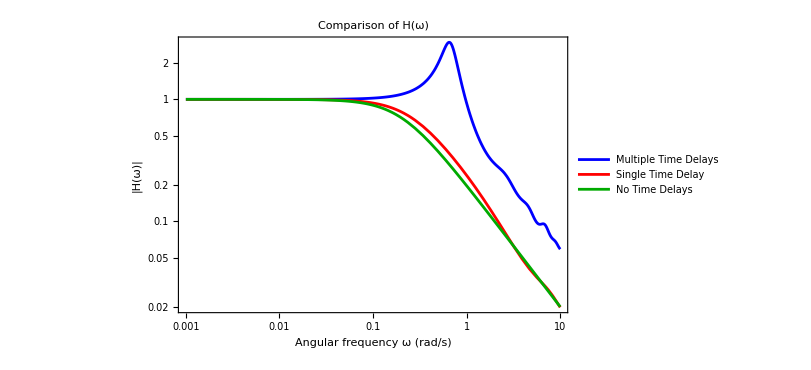

```mathematica
ClearAll["Global`*"];

k=0.2;
(*Magnitude responses*)
H0[ω_]:=k/Sqrt[k^2+ω^2];

H1[ω_]:=Module[{T=1.0},k/Sqrt[(k Cos[ω T])^2+(ω-k Sin[ω T])^2]];

H3[ω_]:=Module[{A,B},A=Sum[Cos[ω n],{n,1,3}];
B=Sum[Sin[ω n],{n,1,3}];
(k*3)/Sqrt[(k A)^2+(ω-k B)^2]];

LogLogPlot[{H3[ω],H1[ω],H0[ω]},{ω,10^-3,10},PlotLegends->Placed[{"Multiple Time Delays","Single Time Delay","No Time Delays"},After],PlotStyle->{Blue,Red,Darker[Green]},Frame->True,FrameLabel->{Style["Angular frequency ω (rad/s)",14],Style["|H(ω)|",14]},PlotRange->All,GridLines->Automatic,ImageSize->600,PlotLabel->Style["Comparison of H(ω)",14,Bold]]
```